```mathematica
Needs["VariationalMethods`"]
Quit;
Clear;
```

```mathematica
Action=Sqrt[r[x]^2+2r'[x]v'[x]-(r[x]^2-m[v[x]])v'[x]^2]; (*Action functional (eqn4.5)*)
```

```mathematica
FullSimplify[Eliminate[{EulerEquations[Action,v[x],x],EulerEquations[Action,r[x],x],r[x]^4/rmin^2==r[x]^2+2 r'[x] v'[x]-(-m[v[x]]+r[x]^2) v'[x]^2},m[v[x]]]] ;(*We can eliminate one of the two EL equaitons using eqn4.6 which can be derived from reparametrrising the action in terms of v and then minimising*)
```

{{r→                             -7
InterpolatingFunction[{{5. 10  , 100.}}, <>],v→                             -7
InterpolatingFunction[{{5. 10  , 100.}}, <>]}}

4.60517

rmin= 0.01

b= 0.9792

vmin= -20.0851

ℓ/2= 23.5044

x @ vmin 23.5044

x @ rmin 23.5044

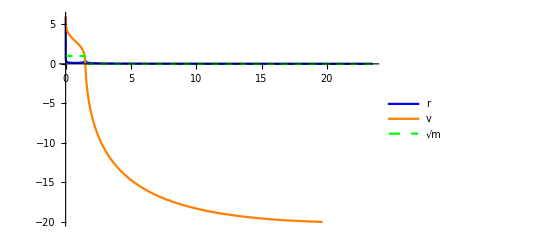

```mathematica
a=1/3; (*Parameter which controls the speed of the perturbation*)
Subscript[m, 0]=1; (*final value of mass function*)
m[v_]:=Subscript[m, 0](Tanh[v/a]+1)/2; (*define the mass function*)
t=6; (*Inital field theory time on boundary*)
r0=0.01; (*Minimum value of r*)
Eqn1=r0^2(r[x]^2+2r'[x]v'[x]-(r[x]^2-m[v[x]])v'[x]^2)-r[x]^4; (*the two equations of motion eqns 4.6, 4.7*)
Eqn2=r[x]^2-r[x]^2 v'[x]^2-r[x]v''[x]+2v'[x]r'[x];
rmax=100;
x0=r0/(2(rmax)^2); (*x0 must be adjusted wrt to r0 and rmax *)
b=0.9792; (*integration const b, b nonzero for r0<1.0, i.e. inside the Vaidya geometry*)
xmax=100;
Sol=NDSolve[{Eqn1==0,Eqn2==0,r[x0]==rmax,v[x0]==t-1/rmax+b/(2 rmax^2),v'[x0]==-rmax/r0+b/r0},{r,v},{x,x0,xmax}]
ℓ=2*x/.Last[Quiet[FindMinimum[v[x]/.Sol,{x,x0,x0,xmax}]]]; (*x=ℓ/2 when r'=v'=0, r[x]=r0,v[x]=v0*)
Print["rmin= ",rmin=First[Quiet[FindMinimum[r[x]/.Sol,{x,ℓ/2,x0,ℓ/2}]]]]
Print["b= ",b]
Print["vmin= ",vmin=First[Quiet[FindMinimum[v[x]/.Sol,{x,ℓ/2,x0,ℓ/2}]]]]
Print["ℓ/2= ",ℓ/2]
Print["x @ vmin ",vmin=x/.Last[Quiet[FindMinimum[v[x]/.Sol,{x,ℓ/2,x0,ℓ/2}]]]]
Print["x @ rmin ",rmin=x/.Last[Quiet[FindMinimum[r[x]/.Sol,{x,ℓ/2,x0,ℓ/2}]]]]
Plot[{Evaluate[r[x]/.Sol],Evaluate[v[x]/.Sol],Evaluate[Sqrt[m[v[x]]]/.Sol]},{x,x0,ℓ/2},PlotStyle->{Blue,Orange,{Dashed,Green}},PlotLegends->{"r","v","√m"},PlotRange->{{x0,ℓ/2},{-20,t}}]
```

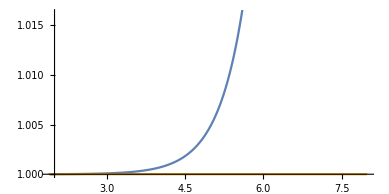

```mathematica
ParametricPlot[{Evaluate[{v[x],r[x]}/.Sol],Evaluate[{v[x],Sqrt[m[v[x]]]}/.Sol]},{x,x0,ℓ/2},AspectRatio->1/2]
```

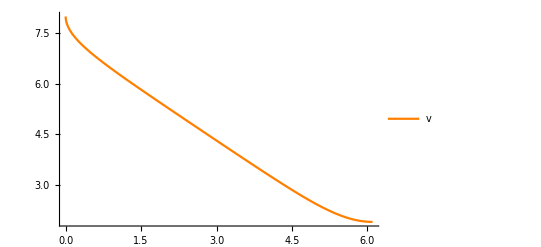

```mathematica
Plot[{Evaluate[v[x]/.Sol]},{x,x0,ℓ/2},PlotRange->All,PlotStyle->{Orange},PlotLegends->{"v"},PlotRange->All]
```

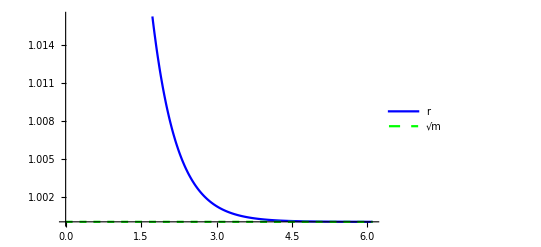

```mathematica
Plot[{Evaluate[r[x]/.Sol],Evaluate[Sqrt[m[v[x]]]/.Sol]},{x,x0,ℓ/2},PlotStyle->{Blue,{Dashed,Green}},PlotLegends->{"r","√m"}]
```

```mathematica
(*This function does the following: takes arguments r0,t,b,Col, where Col defines the Line colour of the output figures.
1. Produce a inital solution Sol to calculate ℓ/2
2. Produce SolL, i.e. the solution for v,r running from -ℓ/2 to -x0
3. Produce 3 plots of the geodesics in the rx,vx,rv planes, output as a list {rx,vx,rv}
4.Integrate to find geodesic length*)
f[r0_,t_,b_,Col_]:=Module[{a,m0,,Eqn1,Eqn2,r,x,v,rmax,xmax,x0,Sol,ℓ,SolL,gr1,gr2,gr3,LInt},
a=1/3;
m0=1;
m[v_]:=m0(Tanh[v/a]+1)/2; (*define the mass function*)
Eqn1=r0^2(r[x]^2+2r'[x]v'[x]-(r[x]^2-m[v[x]])v'[x]^2)-r[x]^4;
Eqn2=r[x]^2-r[x]^2 v'[x]^2-r[x]v''[x]+2v'[x]r'[x];
rmax=100;
x0=r0/(2(rmax)^2);
xmax=100;
Sol=NDSolve[{Eqn1==0,Eqn2==0,r[x0]==rmax,v[x0]==t,v'[x0]==-rmax/r0+b/r0},{r,v},{x,x0,xmax}];
ℓ=2*x/.Last[Quiet[FindMinimum[v[x]/.Sol,{x,x0,x0,xmax}]]];
SolL=NDSolve[{Eqn1==0,Eqn2==0,r[-ℓ/2]==rmax,v[-ℓ/2]==t,v'[-ℓ/2]==-rmax/r0+b/r0},{r,v},{x,-ℓ/2,-x0},"ExtrapolationHandler"->{Indeterminate &}];
gr1=Plot[{Evaluate[r[x]/.SolL],Evaluate[Sqrt[m[v[x]]]/.SolL]},{x,-ℓ/2,ℓ/2},PlotStyle->{Col,{Dashed,Green}},PlotRange->All];
gr2=Plot[Evaluate[v[x]/.SolL],{x,-ℓ/2,ℓ/2},PlotStyle->{Col},PlotRange->All];
gr3=ParametricPlot[{Evaluate[{v[x],r[x]}/.Sol],Evaluate[{v[x],Sqrt[m[v[x]]]}/.Sol]},{x,x0,ℓ/2},AspectRatio->1/GoldenRatio,PlotRange->All,PlotStyle->{Col,{Green,Dashed}}];
LInt=4/r0*NIntegrate[r[x]^2/.SolL,{x,-ℓ/2,-x0}]-2Log[r[-ℓ/2]/.SolL[[1]]];
{gr1,gr2,gr3,ℓ,LInt}
]
```

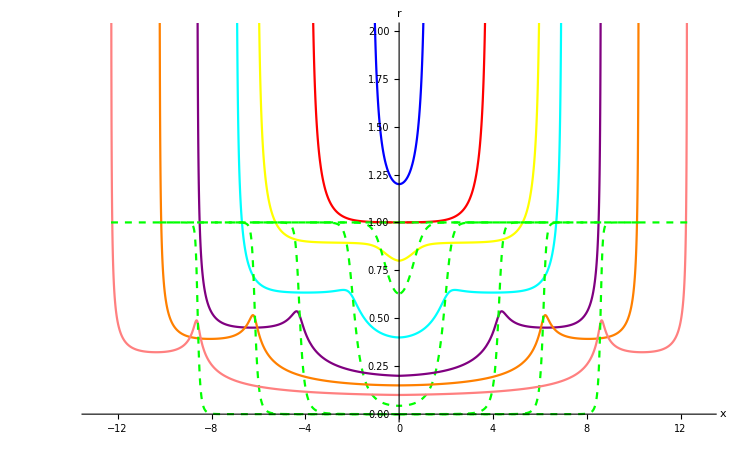

```mathematica
(*Create multiple plots with varying parameters*)
rx1=Part[Quiet[f[1.2,6,0,Blue]],1];
rx2=Part[f[1.0,6,0.001,Red],1];
rx3=Part[f[0.8,6,0.198029,Yellow],1];
rx4=Part[f[0.4,6,0.59405,Cyan],1];
rx5=Part[f[0.2,6,0.79204,Purple],1];
rx6=Part[f[0.15,6,0.841522,Orange],1];
rx7=Part[f[0.1,6,0.89099,Pink],1];
(*Stick the plots together then mirror each plot in the x=0 plane*)
Show[{rx1,rx2,rx3,rx4,rx5,rx6,rx7},{rx1,rx2,rx3,rx4,rx5,rx6,rx7}/.L_Line:>{GeometricTransformation[L,ReflectionTransform[{1,0}]]},PlotRange->{{-13,13},{0.0,2.0}},AxesLabel->{"x","r"}]
```

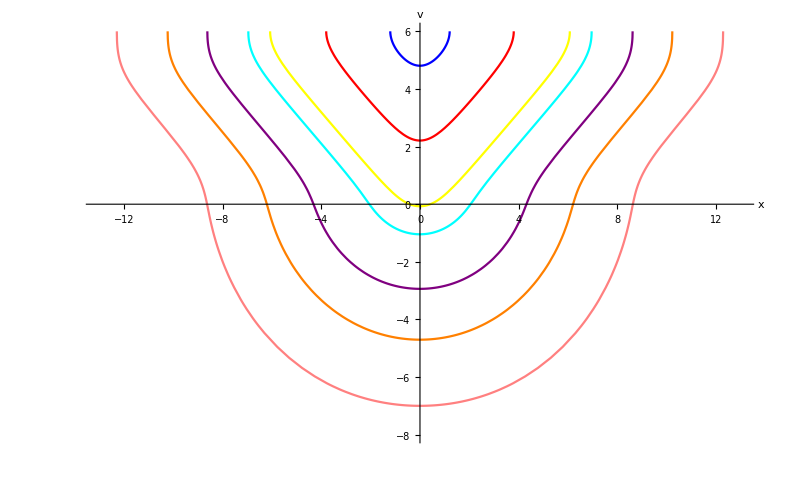

```mathematica
vx1=Part[Quiet[f[1.2,6,0,Blue]],2];
vx2=Part[f[1.0,6,0.001,Red],2];
vx3=Part[f[0.8,6,0.198029,Yellow],2];
vx4=Part[f[0.4,6,0.59405,Cyan],2];
vx5=Part[f[0.2,6,0.79204,Purple],2];
vx6=Part[f[0.15,6,0.841522,Orange],2];
vx7=Part[f[0.1,6,0.89099,Pink],2];

Show[{vx1,vx2,vx3,vx4,vx5,vx6,vx7},{vx1,vx2,vx3,vx4,vx5,vx6,vx7}/.L_Line:>{GeometricTransformation[L,ReflectionTransform[{1,0}]]},PlotRange->{{-13,13},{-8,6}},AxesOrigin->{0,0},AxesLabel->{"x","v"}]
```

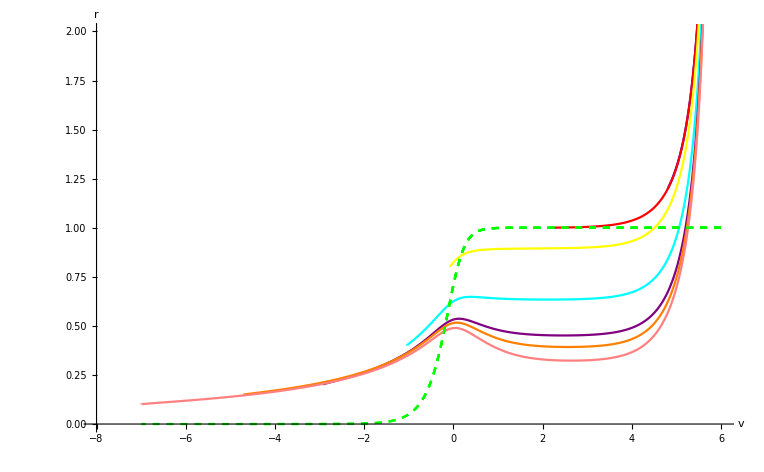

```mathematica
rv1=Part[Quiet[f[1.2,6,0,Blue]],3];
rv2=Part[f[1.0,6,0.001,Red],3];
rv3=Part[f[0.8,6,0.198029,Yellow],3];
rv4=Part[f[0.4,6,0.59405,Cyan],3];
rv5=Part[f[0.2,6,0.79204,Purple],3];
rv6=Part[f[0.15,6,0.841522,Orange],3];
rv7=Part[f[0.1,6,0.89099,Pink],3];

Show[{rv1,rv2,rv3,rv4,rv5,rv6,rv7},PlotRange->{{-8,6},{0.0,2.0}},AxesOrigin->{-8,0},AxesLabel->{"v","r"}]
```

```mathematica
gl0=Quiet[Flatten[f[2,6,0,Blue][[{4,5}]],1]];
gl1=Quiet[Flatten[f[1.2,6,0,Blue][[{4,5}]],1]];
gl2=Flatten[f[1.0,6,0.001,Red][[{4,5}]],1];
gl3=Flatten[f[0.8,6,0.198029,Yellow][[{4,5}]],1];
gl4=Flatten[f[0.4,6,0.59405,Cyan][[{4,5}]],1];
gl5=Flatten[f[0.2,6,0.79204,Purple][[{4,5}]],1];
gl6=Flatten[f[0.15,6,0.841522,Orange][[{4,5}]],1];
gl7=Flatten[f[0.1,6,0.89099,Pink][[{4,5}]],1];
gl8=Flatten[f[0.01,6,0.9792,Pink][[{4,5}]],1];

Lt6=ListCurvePathPlot[{ {1,0},gl3,gl4,gl5,gl6,gl7,gl8},AxesLabel->{"ℓ","L̃(ℓ,t)"},PlotRange->All,AxesOrigin->{0,0},AspectRatio->1/2,InterpolationOrder->3];
β=2Pi;
TherRes=Plot[2Log[β/Pi Sinh[(Pi*ℓ)/β]],{ℓ,0,60}];
VacRes=Plot[2Log[ℓ],{ℓ,0,60}];
Show[{Lt6,TherRes,VacRes},PlotRange->{{0,50},{0,30}}]
```

-Graphics-